```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
Get@"Skew.wl"
```

```mathematica
Get@"Segment.wl"
```

```mathematica
$ContextPath
```

{Segment`,Skew`,Parallel`Debug`Perfmon`,Parallel`Debug`,JLink`,TemplatingLoader`,PacletManager`,System`,Global`}

```mathematica
plot:=ArrayPlot[#,ColorRules->{0->Blue,1->White,2->Red,3->Green},Mesh->All]&(*全黑会画成全白，坑了。用蓝代替黑*)
```

```mathematica
i=Import@"data/01.png"
```

-Graphics-

```mathematica
(*//Flatten[#,1]*)
```

```mathematica
(*i//segmentSmart//(plot/@#&)/@#&;*)
```

```mathematica
(*i//segmentSmart//First//plot/@#&*)
```

```mathematica
(*mtRedTrunBlack[mt_]:=mt/.{x:2..}:>({x}/.{2->0})*)
```

```mathematica
(*RedTrunBlack[mt_]:=mt//Transpose//mtRedTrunBlack//Transpose*)
```

```mathematica
(*i//segmentSmart//First//plot/@#&*)
```

```mathematica
(*i//segmentSmart//First//RedTrunBlack/@#&//plot/@#&*)
(*i//segmentSmart//(RedTrunBlack/@#&)/@#&//(plot/@#&)/@#&*)
```

```mathematica
(*i//segmentSmart//(RedTrunBlack/@#&)/@#&//mergeSplitBy/@#&//plot/@#&*)
```

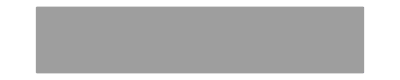
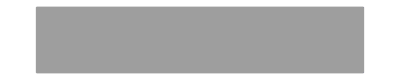
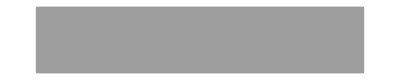
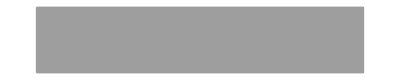
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
i//segmentAndPlot
```

```mathematica
i//segment//First//plot
```

-Graphics-

```mathematica
ocrChinese[i_]:=TextRecognize[i,Language->"Chinese","SegmentationMode"->7]
```

```mathematica
imageBin[mt_]:=Image[mt,"Bit",Magnification->1]//ImageResize[#, Scaled[5]]&
```

```mathematica
(*splitByGreen[mt_]:=mt//Transpose//SplitBy[#,MatchQ[#,{3..}]&]&//Transpose/@#&*)
```

```mathematica
i//segment//First//splitByGreenClean//imageBin/@#&
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
i//segment//First//splitByGreenClean//imageBin/@#&//ocrChinese/@#&
```

{长,久,以,来,!',机,器,视,觉,认,知,íl-,直,是,人,们,研,究,的,热,点,‘l',它,是,研,究,使,用,机,器,或,:í/十,算}